Randomização proporcional ao crescimento de y.

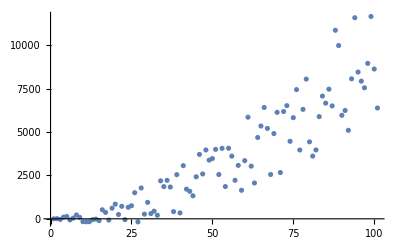

```mathematica
Clear[points1]
points1=Table[x^2+RandomReal[{-40*x,40*x}],{x,0,100,1}];
ListPlot[points1]
```

```mathematica
Manipulate[ListPlot[Table[x^2+RandomReal[{maxrnd*x*-1,maxrnd*x}],{x,0,100,1}],ImageSize->Medium],{maxrnd,0,60}]
```

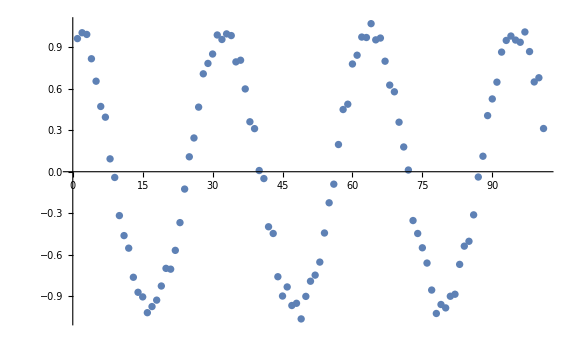

```mathematica
Clear[points2]
points2=Table[Cos[x]+RandomReal[{-0.1,0.1}],{x,0,20,0.2}];
ListPlot[points2,ImageSize->Large]
```

```mathematica
Manipulate[ListPlot[Table[Cos[x]+RandomReal[{maxrnd*-1,maxrnd}],{x,0,20,0.2}],ImageSize->Large],{maxrnd,0,3}]
```

```mathematica
Clear[MakePoints2]
MakePoints2=Function[maxrnd,
	Table[Cos[x]+RandomReal[{maxrnd*-1,0.1}],{x,0,20,0.2}]];
```

Uma série semi-exponencial.

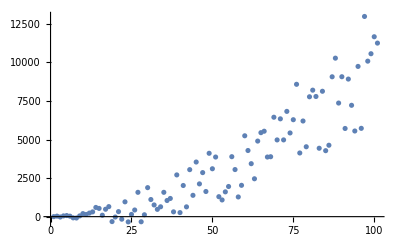

```mathematica
Clear[exp1];
exp1={0.,32.896960274254354,-23.264656131094,48.413892090903175,71.04130636629714,30.71571787217124,-78.2400103320191,-87.31920065999861,47.815364875810246,196.62476367032218,140.72329802485683,231.23106188319366,309.64887890045566,597.9161180482959,534.4017554894099,92.12528425774008,480.88506962469,649.8705784591684,-320.7181849098183,-24.702074266884892,326.1435564229646,-163.85167012602165,961.1304491019464,-340.3394164950407,143.82836032124305,431.42986255900723,1578.4007056162009,-331.77117810482605,121.88891793858875,1881.7183407592584,1111.0316516201424,759.0700853285616,473.93543584330837,639.1504820253281,1578.0609807200726,1047.2069391937493,1180.2116238147746,311.38953864697305,2707.5507803101746,262.25587440577783,2020.8812908511163,635.1455123643627,3049.2598696308205,1383.6834126333952,3543.357458164154,2124.8960870507462,2856.655474239441,1631.1153162436922,4110.062929401679,3106.6213600204674,3867.8678376996013,1294.7531440598386,1083.6785921528563,1608.3102976058944,1955.8469590368295,3890.0753552324204,3054.696673072499,1278.2091595299044,2032.616653686001,5245.8239752182435,4290.528814447963,3436.116038186936,2456.9595315230745,4902.6001502039,5447.817208449704,5541.796735266875,3867.8474375105534,3887.3461606785577,6448.922337756563,4977.387455625809,6345.161243921662,4978.330020108655,6828.175823249763,5429.309086348778,6287.837027392425,8585.229511620408,4130.349965977841,6204.706332728636,4533.579247688535,7775.620642994407,8205.230927406965,7794.1014083145965,4437.418969666293,8134.088842539819,4279.5519850953215,4631.983781903142,9072.85484720021,10281.716367605424,7369.244378403393,9076.359273899754,5720.2606021228985,8924.938288695506,7223.622960159175,5556.1948215725915,9745.719646746831,5729.048433533139,12986.045596693588,10087.379834632671,10568.321810409445,11670.140893906295,11258.291964960259};
ListPlot[exp1]
```

Descobrir a relação de y com x.

Comparar cada y com a f(x) modelo no mesmo x. Minimizar a soma das diferenças.
Por exemplo:
f(x)=x^2
Em x=30, y=900.
Para isso é preciso atribuir x para os valores da série.
O índice (do list) começa em 1.

```mathematica
exp1[[30]]
```

1881.72

Podemos usar os índices como x por enquanto.

```mathematica
Clear[fexp1model1]
fexp1model1=Function[x,x^2];
```

```mathematica
exp1[[30]]-fexp1model1[30]
```

1248.38

Diferença significativa. Precisamos ver a média das diferenças.
Poderíamos discretizar (samplear?) a f modelo e comparar em índices.

```mathematica
Clear[exp1model1]
exp1model1=Table[fexp1model1[x],{x,0,100,1}]
```

{0,1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400,441,484,529,576,625,676,729,784,841,900,961,1024,1089,1156,1225,1296,1369,1444,1521,1600,1681,1764,1849,1936,2025,2116,2209,2304,2401,2500,2601,2704,2809,2916,3025,3136,3249,3364,3481,3600,3721,3844,3969,4096,4225,4356,4489,4624,4761,4900,5041,5184,5329,5476,5625,5776,5929,6084,6241,6400,6561,6724,6889,7056,7225,7396,7569,7744,7921,8100,8281,8464,8649,8836,9025,9216,9409,9604,9801,10000}

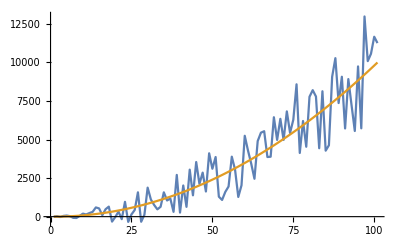

```mathematica
ListLinePlot[{exp1,exp1model1}]
```

```mathematica
exp1[[30]]-exp1model1[[30]]
```

1040.72

Todos...

```mathematica
exp1model1-exp1
```

{0.,-31.897,27.2647,-39.4139,-55.0413,-5.71572,114.24,136.319,16.1846,-115.625,-40.7233,-110.231,-165.649,-428.916,-338.402,132.875,-224.885,-360.871,644.718,385.702,73.8564,604.852,-477.13,869.339,432.172,193.57,-902.401,1060.77,662.111,-1040.72,-211.032,201.93,550.065,449.85,-422.061,177.793,115.788,1057.61,-1263.55,1258.74,-420.881,1045.85,-1285.26,465.317,-1607.36,-99.8961,-740.655,577.885,-1806.06,-705.621,-1367.87,1306.25,1620.32,1200.69,960.153,-865.075,81.3033,1970.79,1331.38,-1764.82,-690.529,284.884,1387.04,-933.6,-1351.82,-1316.8,488.153,601.654,-1824.92,-216.387,-1445.16,62.67,-1644.18,-100.309,-811.837,-2960.23,1645.65,-275.706,1550.42,-1534.62,-1805.23,-1233.1,2286.58,-1245.09,2776.45,2593.02,-1676.85,-2712.72,374.756,-1155.36,2379.74,-643.938,1240.38,3092.81,-909.72,3295.95,-3770.05,-678.38,-964.322,-1869.14,-1258.29}

```mathematica
Mean[exp1model1-exp1]
```

-80.596

```mathematica
Total[exp1model1-exp1]
```

-8140.2

Gerando nova série com ruído linear...

```mathematica
Manipulate[
pts=Table[x^2+RandomReal[{maxrnd*50*-1,maxrnd*50}],{x,0,100,1}];
ListPlot[pts,ImageSize->Medium],
{maxrnd,0,60},
Dynamic["Std. dev.: "<>ToString[StandardDeviation[pts]]]
]
```

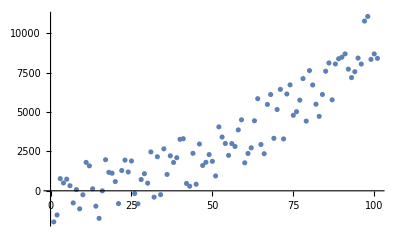

```mathematica
Clear[points1b]
maxrnd=40;
points1b=Table[x^2+RandomReal[{-50*maxrnd,50*maxrnd}],{x,0,100,1}];
ListPlot[points1b]
```

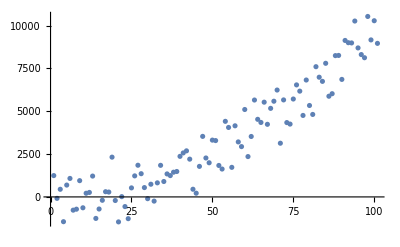

```mathematica
Clear[exp1b]
exp1b={1244.87424194898,-84.07549668914908,446.196305181199,-1445.56143785746,691.7253234604159,1079.512849107322,-772.0394824305295,-715.4230778863748,949.5619808219471,-634.4450461349288,214.0826529340302,261.80841278797925,1216.932607167183,-1254.3873542357223,-705.6308022026569,-196.1107028344004,303.84524463848356,283.490928440463,2321.607100671051,-209.09335242606994,-1457.9528099067948,15.698955434896561,-563.595983877849,-1269.3642875359901,527.1758285172655,1228.3307570996494,1848.9229019542563,1355.2573579091522,544.9410927327226,-102.72116444955009,740.3186761160496,-244.8525747161757,821.625866090827,1843.6534815803043,899.9709595506529,1342.3664042454884,1244.7163921065767,1442.6187117379768,1483.8808519152353,2367.4702382465903,2567.4162556504352,2689.0151764137117,2204.661970739621,448.0435733482964,216.8237827710709,1782.4212642450093,3533.7986397397763,2272.2193838321655,1993.4283117021396,3315.912058991301,3288.779528755954,1836.246206515736,1627.777823042592,4411.852085447112,4054.149358629752,1726.3822902979282,4151.099169114793,3210.681375624922,2936.9770732570996,5102.441058241816,2355.0481193807445,3527.790767320227,5655.596275031297,4529.178812425745,4346.91432349158,5530.375435778425,4237.76432132417,5169.565996768326,5586.071883848494,6238.510612683809,3134.5682081166206,5661.846749056337,4339.625473041178,4251.212385776947,5714.778540958786,6538.698970475642,6173.923795745773,4756.123194591116,6823.513808723065,5336.59445468462,4814.385741044567,7601.176251062999,6987.024090564625,6744.799575502757,7799.232146822729,5877.0264661557085,6024.6055488778175,8247.877769714596,8258.305544358993,6859.517481518431,9132.841145443253,9001.729175113987,8988.087300578318,10266.137031833247,8697.430703038444,8308.61924597661,8124.460280667454,10533.323541366877,9164.49320485329,10283.748430572434,8962.765337901586};
ListPlot[exp1b]
```

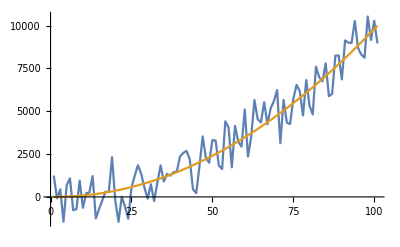

```mathematica
ListLinePlot[{exp1b,exp1model1}]
```

Se o total é a soma das diferenças, este é o número que devemos minimizar. (Ou a média também.)

Supondo que traçamos uma curva qualquer para acompanhar o dado. Podemos avaliar a soma ou média das distâncias (tentando igualar a zero). Para este dado (agora que vimos que x^2 fornece um bom baseline), podemos introduzir uma variável randômica:

Y=x^2+A

Parâmetro (letra grega): constante de valor desconhecido.

Vamos supor alguns valores para A. Que tipo de valor uma variável randômica pode ter? Nenhum fixo... Precisa ter um range, e probabilidades de cair em cada valor possível — ou seja, uma distribuição.

E como a distribuição é especificada?

A distribuição do RandomReal, anyway, é uniforme.

Integração: "(...) a smooth curve called a probability density function, usually abbreviated to pdf. A pdf must take only non-negative values, and the total area under the curve must be one. Then, the area under the curve between any two values, a and b, say, gives the probability that the outcome will take a value somewhere between a and b.”1

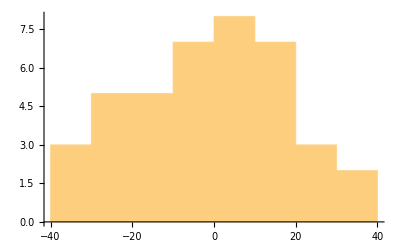
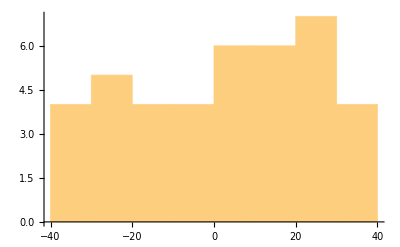
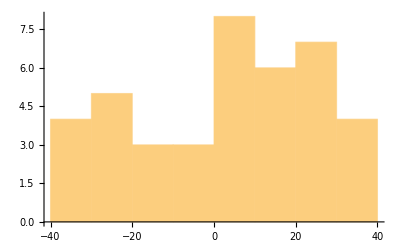
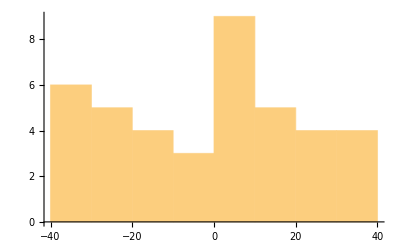
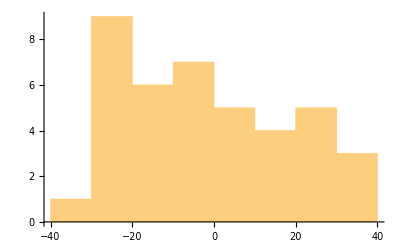
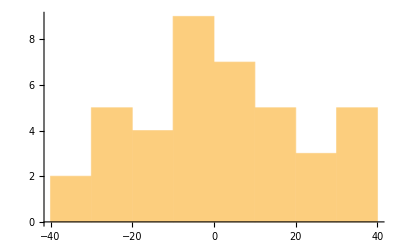
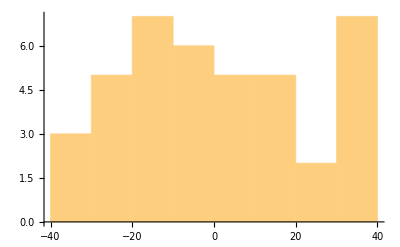
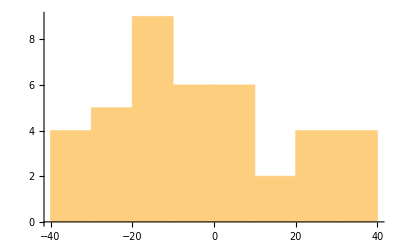

```mathematica
Table[Histogram[Table[RandomVariate[UniformDistribution[{-40,40}]],40],{-40,40,10},ImageSize->Tiny],8]
```

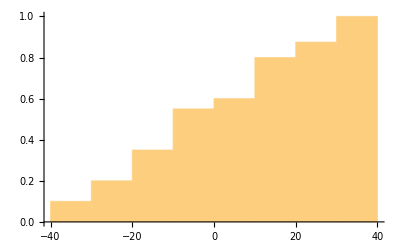
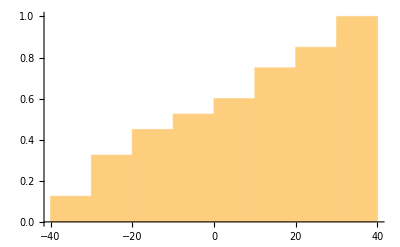
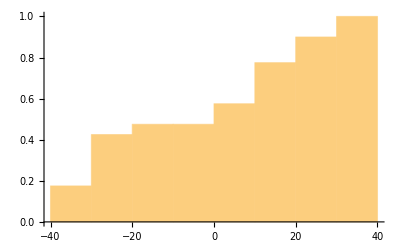
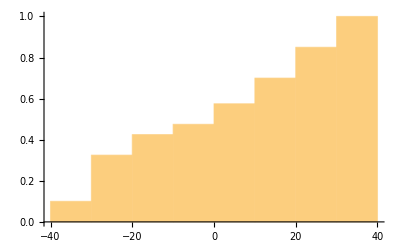
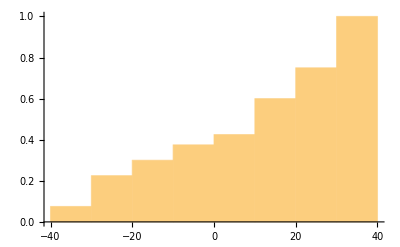
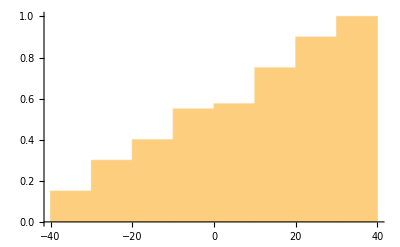
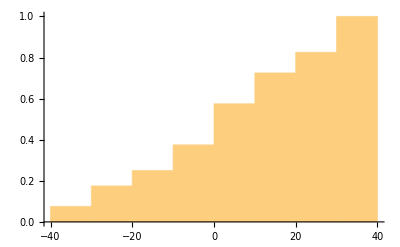
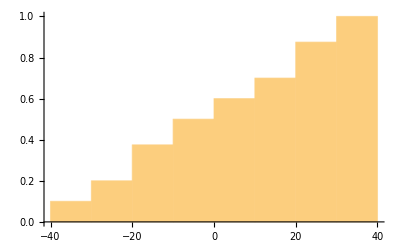

```mathematica
Table[Histogram[Table[RandomVariate[UniformDistribution[{-40,40}]],40],{-40,40,10},"CDF",ImageSize->Tiny],8]
```

Ainda não estou especificando as distribuições, apenas instanciando... as distribuições são (internamente) funções.

Distribuição normal:
ϕ(x)=1/(√(2 πσ^2))ⅇ-(x-μ)^2/(2 σ^2), onde
μ= média
σ= variância

```mathematica
Clear[ϕ0]
ϕ0=Function[{x,μ,σ},1/(√(2π*σ^2))ⅇ^(-(x-μ)^2/(2 σ^2))]
```

Function[{x,μ,σ},(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π σ^2))]

```mathematica
Manipulate[Plot[ϕ0[x,μ,σ],{x,-10,10},PlotRange->{{-10,10},{0,0.5}},ImageSize->Medium],{{μ,0},-10,10,.01},{{σ,1},0.5,5,.01}]
```

A média só desloca. É a variância que é interessante.
Quanto menor a variância, (logicamente) mais uniforme a distribuição.

“Every normal distribution is a version of the standard normal distribution whose domain has been stretched by a factor σ (the standard deviation) and then translated by μ (the mean value).”2

Distribuição normal:  “(...) the number of cancer-related deaths in the UK next year; strictly this must be a finite number, but its upper bound is hard to determine exactly. For a variable like this, the usual strategy for describing its statistical properties is to specify a probability distribution that allows arbitrarily large outcomes, but with vanishingly small probabilities.”3 (O tail-end.)

Variações:

ϕ(x)=1/(√(2π))ⅇ-1/2 x^2. Distribuição normal “padrão” com μ=0, σ=1.

```mathematica
Clear[ϕ1,ϕ2,ϕ3]
ϕ1=Function[x,1/(√(2π))ⅇ^(-x^2/2)]
ϕ2=Function[x,(ⅇ^(-x^2))/(√π)]
ϕ3=Function[x,ⅇ^(-π*x^2)]
```

Function[x,(ⅇ^(-x^2/2))/(√(2 π))]

Function[x,(ⅇ^(-x^2))/(√π)]

Function[x,ⅇ^(-π x^2)]

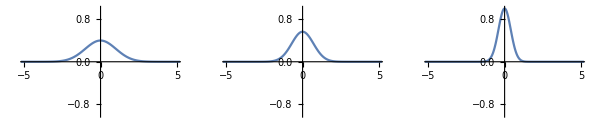

```mathematica
GraphicsRow[{
Plot[ϕ1[x],{x,-10,10},PlotRange->{{-5,5},{-1,1}},ImageSize->Small],
Plot[ϕ2[x],{x,-10,10},PlotRange->{{-5,5},{-1,1}},ImageSize->Small],
Plot[ϕ3[x],{x,-10,10},PlotRange->{{-5,5},{-1,1}},ImageSize->Small]
}]
```

Erro (parábola): a diferença entre a parábola e esta curva era x participar na base ou no expoente na função.

“Every normal distribution is the exponential of a quadratic function:”4
f(x)=ⅇ^(ax^2+bx+c) (onde a<0 e c=b^2/(4a)+(ln(-a/π))/2).

τ: constante de precisão (recíproco/inverso da variância: 1/σ)
μ: média

```mathematica
Clear[ϕ4,ϕ5]
ϕ4=Function[{x,τ,μ},√(τ/(2π))ⅇ^((-τ(x-μ)^2)/2)]
```

Function[{x,τ,μ},√(τ/(2 π)) ⅇ^(1/2 (-τ) (x-μ)^2)]

```mathematica
Manipulate[Plot[ϕ4[x,τ,μ],{x,-10,10},PlotRange->{{-10,10},{0,.5}},ImageSize->Medium],{{τ,1},0.01,1,.01},{{μ,0},-10,10,.01}]
```

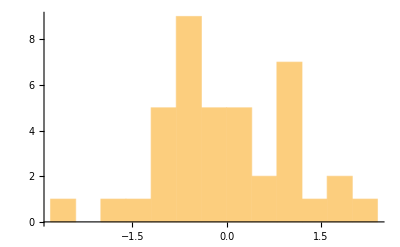
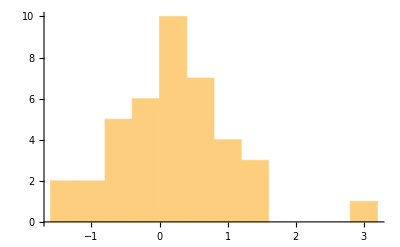
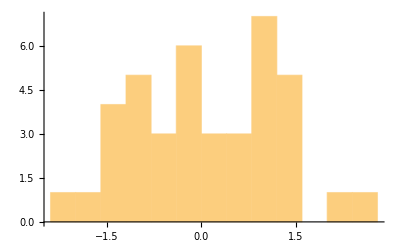
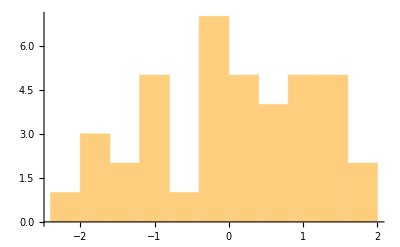
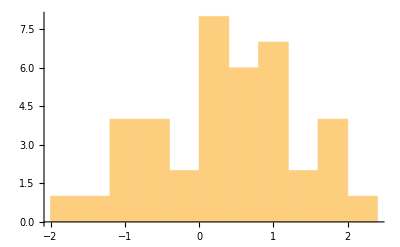
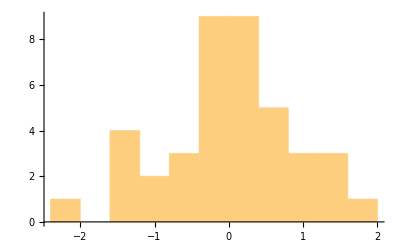
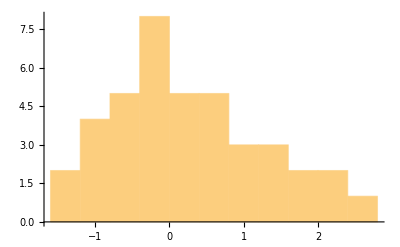
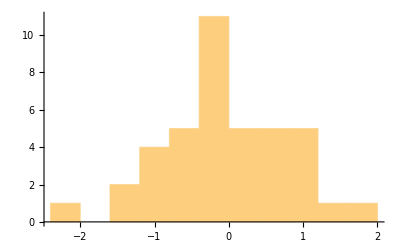

```mathematica
Table[Histogram[Table[RandomVariate[NormalDistribution[]],40],{.4},ImageSize->Tiny],12]
```

“A discrete probability distribution can be encoded by a discrete list of the probabilities of the outcomes, known as a probability mass function. A continuous probability distribution is typically described by probability density functions (with the probability of any individual outcome actually being 0). The normal distribution is a commonly encountered continuous probability distribution.”5

Integração: “The values of the pdf (as opposed to those of the pmf) are not probabilities as such: a pdf must be integrated over an interval to yield a probability.”6
“(...) a smooth curve called a probability density function, usually abbreviated to pdf. A pdf must take only non-negative values, and the total area under the curve must be one. Then, the area under the curve between any two values, a and b, say, gives the probability that the outcome will take a value somewhere between a and b.”7

Isso é claro, a pmf fornece as probabilidades como soma das áreas dos retângulos. A pdf é uma curva. (E se aproximarmos a pdf apenas?)

Supor variáveis randômicas erradas para ver os resultados.

A variável certa é: ϕ(x)=1 com domínio em -40<x<40.

O “intervalo” da variável randômica é o domínio da função definidora.

#### Modelo 1

```mathematica
Clear[exp1ϕ1]
exp1ϕ1=ProbabilityDistribution[Function[x,1][x],{x,-40,40}]
```

ProbabilityDistribution[1,{x,-40,40}]

```mathematica
Table[RandomVariate[exp1ϕ1],20]
```

{30.0984,9.14555,-14.1705,-22.8391,32.9483,-2.42389,-36.5842,-17.203,35.6297,-19.3011,20.5506,-27.0192,12.1335,-2.7879,-5.90197,-14.5735,32.3403,-24.8704,-33.4424,29.9531}

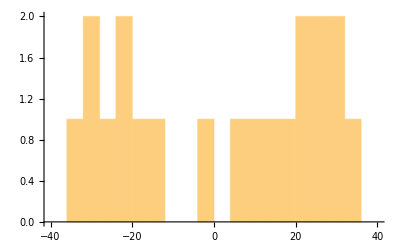
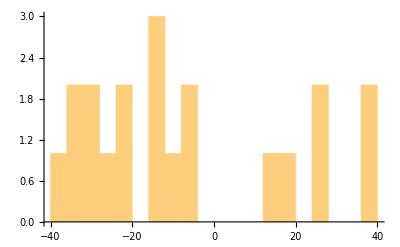
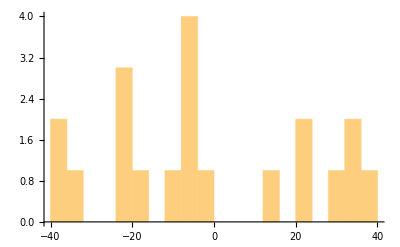
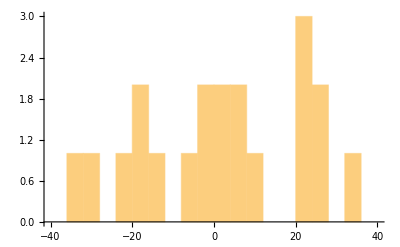
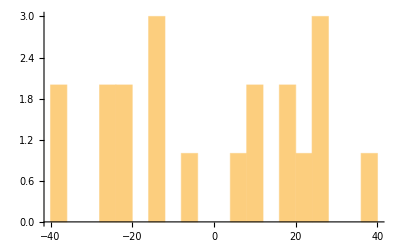
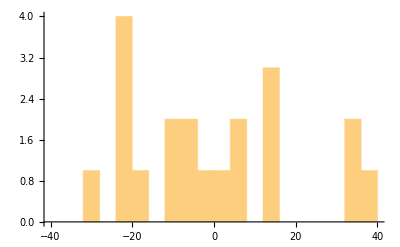
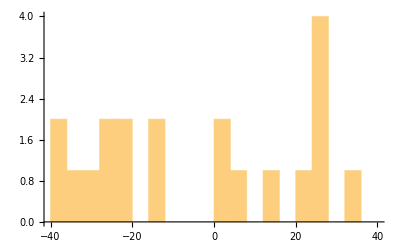
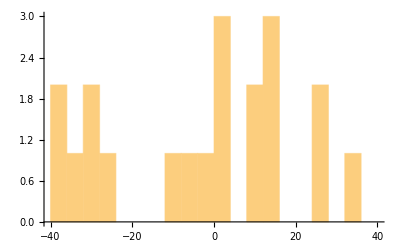

```mathematica
Table[Histogram[Table[RandomVariate[exp1ϕ1],20],{-40,40,4},ImageSize->Tiny],12]
```

Os números ficam relativamente uniformes. É que os máximos estão em ≈4.

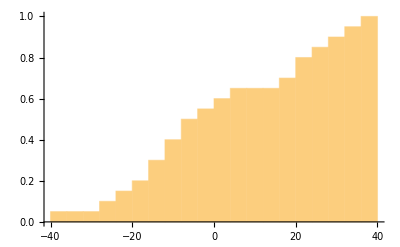
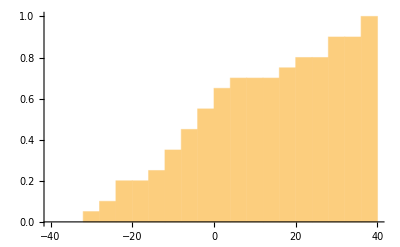
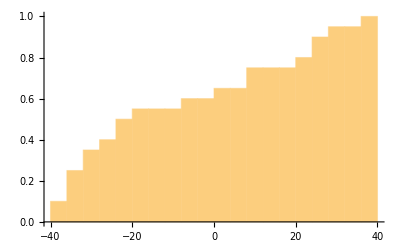
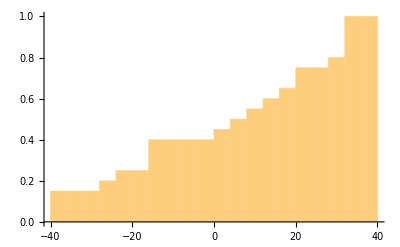
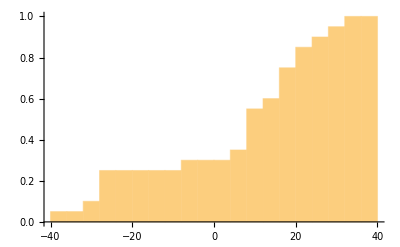
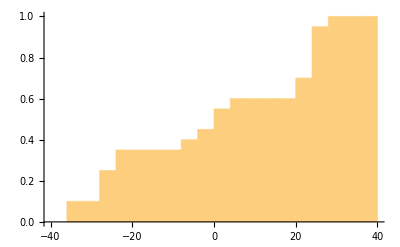
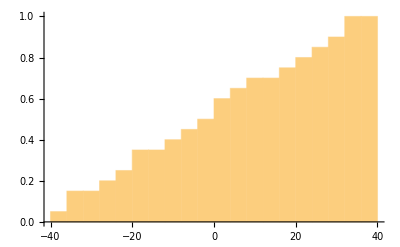
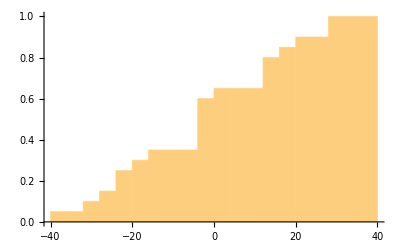

```mathematica
Table[Histogram[Table[RandomVariate[exp1ϕ1],20],{-40,40,4},"CDF",ImageSize->Tiny],12]
```

Agora criar outras erradas.

```mathematica
Clear[pdhistos]
pdhistos=Function[{pd,binfrom,binto,binsize,qty},
	Table[Histogram[RandomVariate[pd,binto-binfrom],{binfrom,binto,binsize},
		ImageSize->Tiny],qty]];
```

#### Modelo 2

O valor é o domínio (x). A probabilidade é a imagem (y).
Ou seja, não fazem sentido valores negativos para a imagem. Toda função deveria ser 0+.

Neste caso, ou faço uma função modular, ou piecewise.

Está faltando o componente ×x na variável randômica. Só que isso é dependente da função... teremos que simular incorporando o grau da função na definição da randômica.
O problema é que o domínio da distribuição também acompanha x. Tem duas alternativas
1) Cada ponto na série define uma função probabilidade com x como componente... uma probabilidade dependente. Verificar o conceito depois.
2) Alteramos o “fenômeno” para ter “ruído” linear por agora.

A imagem das funções das variáveis aleatórias devem ir de 0 a 1. Como “relativizar” a este intervalo? Além disso, a soma da área deve ser 1. Ou seja, usar funções arbitrárias cria distribuições inválidas. Terei de criar as distribuições pelo Manipulate. Irei criar uma distribuição exponencial para imitar este caso.

```mathematica
Clear[λ0]
λ0=Function[{x,λ},Piecewise[{{λ*ⅇ^(-λ*x),x≥0},{0,x<0}}]]
λ0[10,10]
```

Function[{x,λ},Piecewise[{{λ ⅇ^(-λ x), x≥0}, {0, x<0}}]]

10/ⅇ^100

```mathematica
Manipulate[Plot[λ0[x,λ],{x,-20,20},PlotRange->{{-20,20},{0,1}},ImageSize->Medium],{{λ,0.29},0.01,1,.01}]
```

O problema é que esta distribuição nesta forma não é deslocada e o deslocamento não é simples.
Essas funções têm domínio infinito para o(s) lado(s) com “tail”... Mas dá para “cropar” a imagem da linear para 20 também, usar qualquer uma das duas.

O histograma “imita” o formato da função da distribuição. Mas os eixos não “são a mesma coisa”: no histograma, o eixo y tem os valores gerados e, no eixo x, ...?

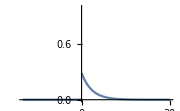

{219.659,1206.71,729.922,369.698,601.465,547.536,19.553,305.196,684.44,215.503,163.274,1269.12,411.061,576.239,85.722,820.902,429.772,29.2015,339.954,83.2262,361.013,149.535,172.121,440.485,364.107}

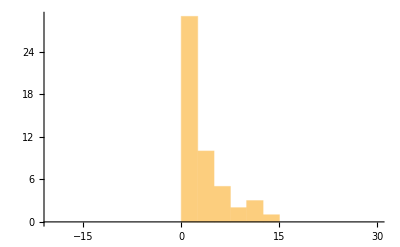
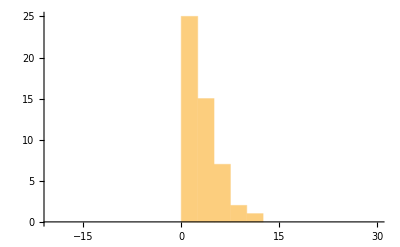
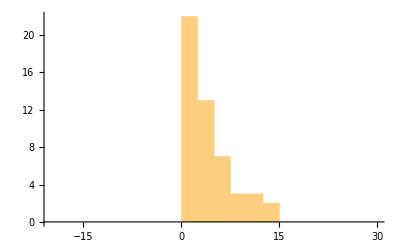
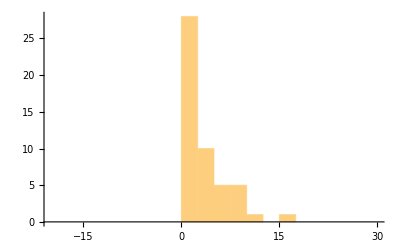
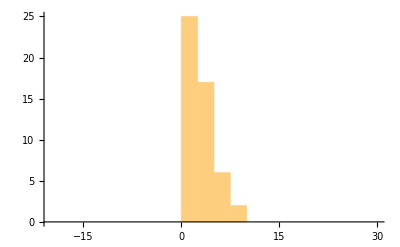
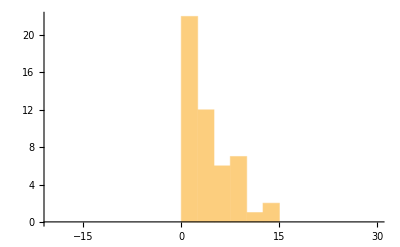
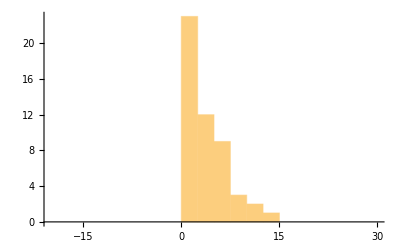
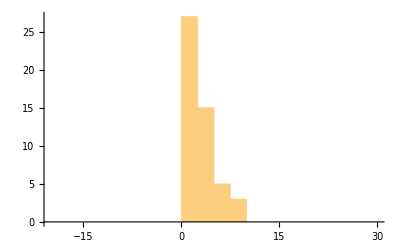

```mathematica
Clear[f,exp1λ0]
f=λ0[x,0.29];
Plot[f,{x,-20,30},PlotRange->{{-20,30},{0,1}},ImageSize->Small]
exp1λ0=ProbabilityDistribution[f,{x,-20,20}];
RandomVariate[exp1λ0,25]*100
pdhistos[exp1λ0,-20,30,2.5,16]
```

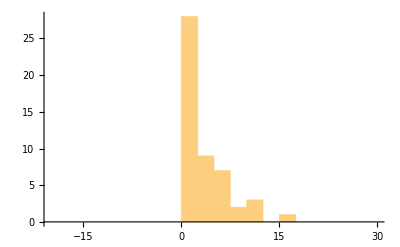
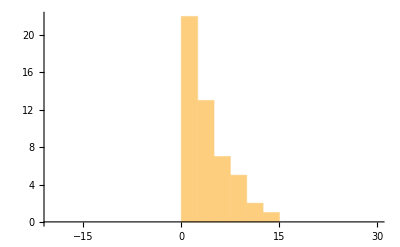
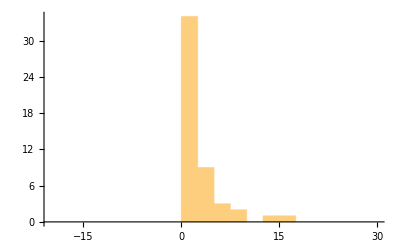
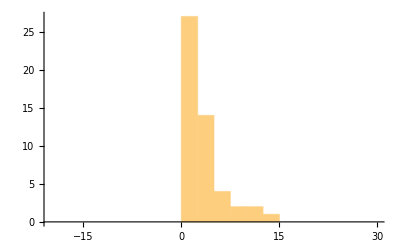
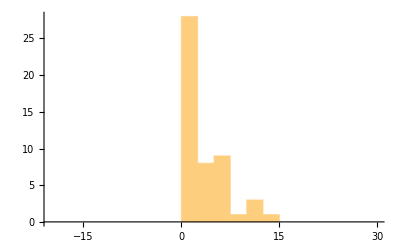
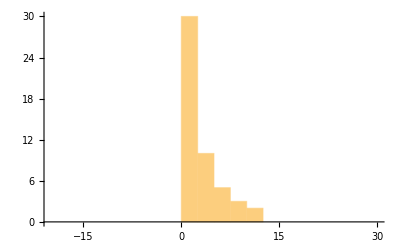
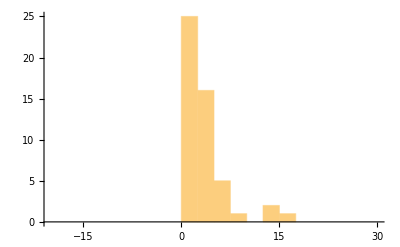
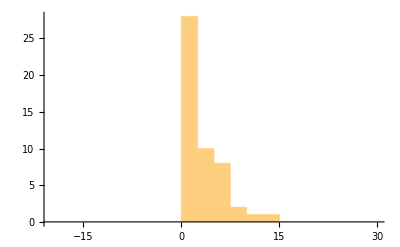

```mathematica
{53.93704642007098,97.01729297965684,97.13977946406729,314.0676767080434,67.6758201021542,188.10817539770585,501.34818183458094,78.09059895020968,108.19778444830526,331.2147942366284,108.82309314954296,142.18042480265785,262.01073835320017,830.6028310787516,113.56663174391315,256.4344040636772,50.52626180857285,232.26042748283095,226.96681454537355,198.44608507807263,448.47767989590545,735.5179208084074,64.30122525802435,146.46880668600488,280.55245258111336}
```

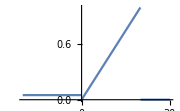

{1185.05,1155.79,216.681,405.419,1122.26,1462.41,1937.,1252.01,-175.097,1637.82,-1119.62,1771.6,717.675,-1676.25,1171.06,1141.8,902.915,1232.29,1048.82,1979.7,1272.4,1293.44,1143.43,1210.04,1437.26}

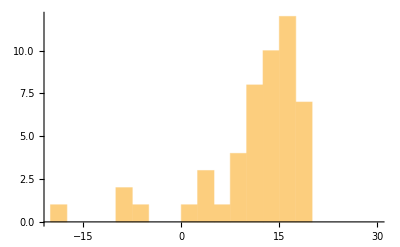
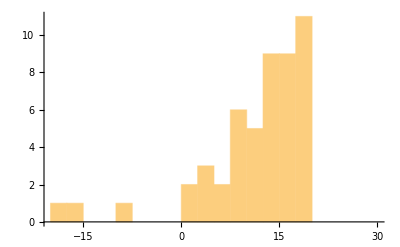
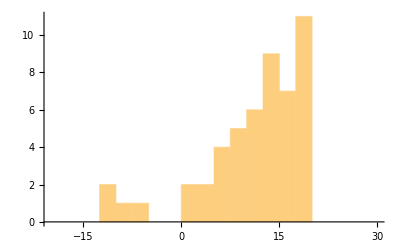
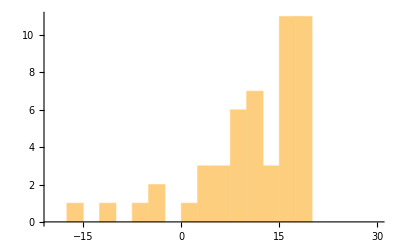
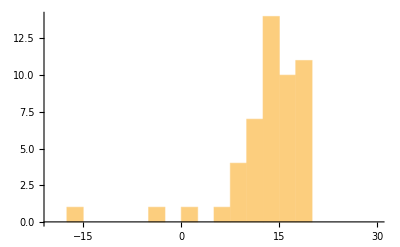
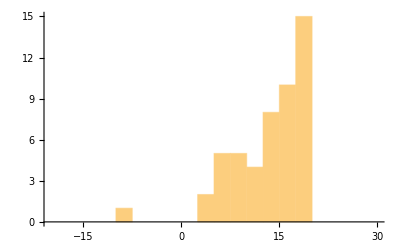
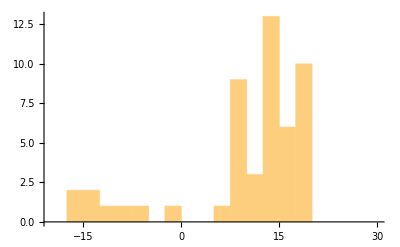
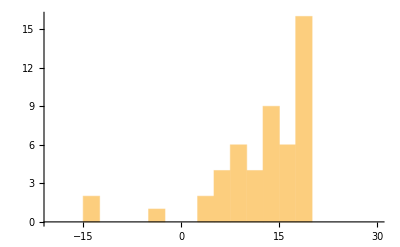

```mathematica
Clear[f,exp1ϕ2]
f=Piecewise[{{0.05,x≤0},{x/20,x>0&&x≤20},{0,x>20}}];
Plot[f,{x,-20,30},PlotRange->{{-20,30},{0,1}},ImageSize->Small]
exp1ϕ2=ProbabilityDistribution[f*maxrnd,{x,-20,20}];
RandomVariate[exp1ϕ2,25]*100
pdhistos[exp1ϕ2,-20,30,2.5,16]
```

A distribuição é exatamente a mesma coisa que a função definidora... (em termos de valores retornados). Portanto o intervalo da distribuição e domínio da função são teoricamente coincidentes (para representar a variação na variável randômica).
Neste primeiro modelo, estamos intencionalmente usando um domínio de intervalo menor que o da variável correta, e apenas no sentido positivo.

#### Modelo 3

Uma exponencial invertida também com o domínio menor.

```mathematica
(*Clear[f,exp1ϕ3]
f=Function[x,Piecewise[{{-x^(1/2),x≥0},{0,x<0}}]];
exp1ϕ3=ProbabilityDistribution[f[x],{x,-10,10}];
Plot[f[x],{x,-10,10},ImageSize->Small]*)
```

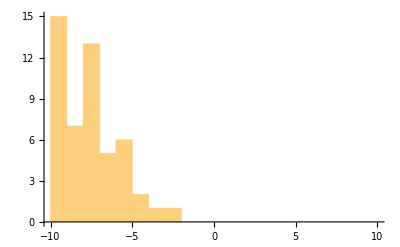
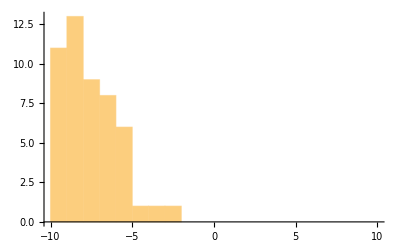
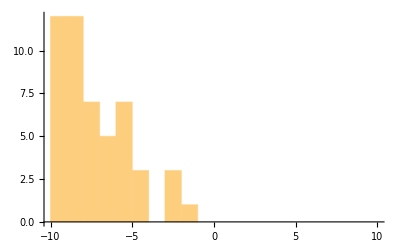
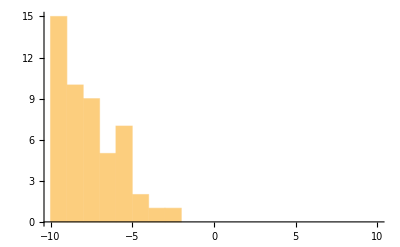
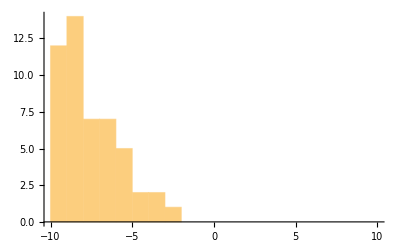
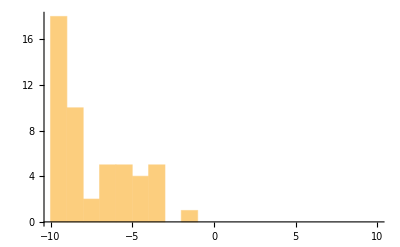
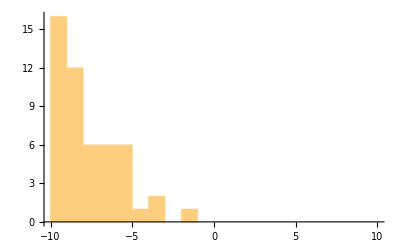
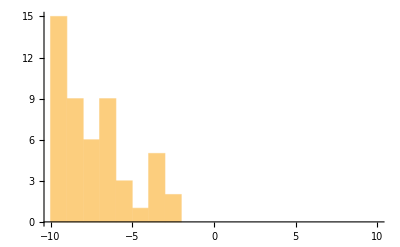

```mathematica
(*pdhistos[exp1ϕ3,0,100,1,16]*)(*Quebra*)
```

### Integrar

Integrar ambas como variável randômica de points1 e comparar as variações nas distâncias.

```mathematica
(*TODO: Dicretize retorna uma lista com length steps + 1. Seria legal corrigir para 
retornar lista com length steps e retirar os Length[...]-1 das chamadas de Discretize 
que passam o tamanho de uma lista gerada por Discretize como parâmetro steps.*)
Clear[Discretize]
Discretize=Function[{f,steps,x1},Table[f[x],{x,0,x1,Floor[x1/steps]}]];
Table[x^3,{x,0,100,10}]
Discretize[Function[x,x^3],10,100]
```

{0,1000,8000,27000,64000,125000,216000,343000,512000,729000,1000000}

{0,1000,8000,27000,64000,125000,216000,343000,512000,729000,1000000}

#### Modelo 1

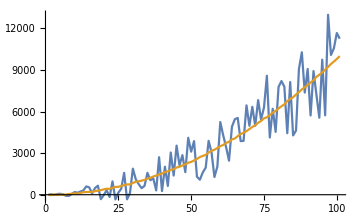

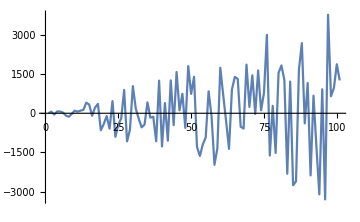

```mathematica
Clear[fexp1model1,exp1model1,exp1model1diff]
(*model1=Function[x,x^2+RandomReal[{-40*x,40*x}]]*)
fexp1model1=Function[x,x^2+RandomVariate[exp1ϕ1]];
exp1model1=Discretize[fexp1model1,100,100];
exp1model1diff=exp1-exp1model1;
ListLinePlot[{exp1,exp1model1},ImageSize->Medium]
ListLinePlot[exp1model1diff,ImageSize->Medium]
```

#### Modelo 2

Esse modelo engloba dois modelos, um exponencial e um linear.

```mathematica
m=Directive[Opacity[1],Thickness[.01]];
s=Directive[{Opacity[.7]}];
```

```mathematica
exp1ϕ2
```

ProbabilityDistribution[40 (Piecewise[{{0.05, x≤0}, {x/20, x>0&&x≤20}, {0, True}}]),{x,-20,20}]

```mathematica
Plot[{x^2,x^2+RandomVariate[exp1ϕ2]*100},{x,0,100},PlotStyle->{m,s},PlotLegends->{"variable","random variable"}]
```

-Graphics-

```mathematica
Discretize[Function[x,x^2+RandomVariate[exp1ϕ2]*100],100,100]
```

{1754.06,1022.67,1584.27,676.094,-1466.59,1176.81,1720.88,1649.46,1799.01,984.223,1077.02,-1047.44,933.075,1434.13,1971.79,835.687,2147.7,1735.01,1602.12,1477.21,2224.7,1979.45,2120.87,1766.67,2108.78,1448.37,1444.58,231.966,2740.82,1181.61,2656.,187.353,1506.13,2236.44,2587.7,196.05,3136.,5.50086,3095.,3179.63,3061.8,2896.24,2653.49,2959.38,3362.6,2739.7,3822.3,2608.47,2981.86,1447.52,3425.92,3375.82,3412.67,3846.15,4714.2,3641.09,4314.73,2104.69,4753.65,4714.99,4812.36,4898.12,4512.79,5622.29,5944.37,5226.15,4556.51,5980.46,5878.43,5805.7,5767.19,6978.16,7046.64,6437.92,6440.07,7537.1,6903.35,7266.31,6750.02,7334.13,6950.29,7033.34,7691.1,6653.47,8456.79,8187.95,8247.07,9502.47,8805.96,8973.31,9649.97,9426.6,9398.64,10403.4,10432.4,10709.,9820.06,10588.,10594.4,11703.5,11170.4}

```mathematica
ListLinePlot[Discretize[Function[x,x^2+RandomVariate[exp1ϕ2]*100],100,100]]
```

-Graphics-

```mathematica
Clear[exp1model2ϕ,exp1model2ϕdiff]
exp1model2ϕ=Discretize[Function[x,x^2+(RandomVariate[exp1ϕ2]-10)*100],100,100];
exp1model2ϕdiff=exp1b-exp1model2ϕ;
ListLinePlot[{exp1b,exp1model2ϕ},ImageSize->Medium,PlotLegends->{"data","model"}]
ListLinePlot[exp1model2ϕdiff,ImageSize->Medium,PlotLabel->"difference"]
```

-Graphics-

-Graphics-

```mathematica
Mean[exp1model2ϕdiff]
```

-248.851

```mathematica
Plot[{x^2,x^2+RandomVariate[exp1λ0]*100},{x,0,100},PlotStyle->{m,s},PlotLegends->{"variable","random variable"}]
```

-Graphics-

```mathematica
Clear[exp1model2λ,exp1model2λdiff]
exp1model2λ=Discretize[Function[x,x^2+(RandomVariate[exp1ϕ2]-10)*100],100,100];
exp1model2λdiff=exp1b-exp1model2λ;
ListLinePlot[{exp1b,exp1model2λ},ImageSize->Medium,PlotLegends->{"data","model"}]
ListLinePlot[exp1model2λdiff,ImageSize->Medium,PlotLabel->"difference"]
```

-Graphics-

-Graphics-

```mathematica
Mean[exp1model2λdiff]
```

51.9879

Este segundo é mais aproximado.

As perguntas são...
1) Estruturas contínuas vs. discretas... qual das duas melhor para trabalhar? Requer conversão constante de um para o outro?
2) Porquê o domínio das distribuições é especificado com x>0? E para especificar com probabilidades em valores negativos, é preciso deslocar depois os valores gerados? Ou seja, há um passo adicional de transformação das distribuições?

No Cosinor, variarei uma curva cossena sobre sobre os dados acompanhando as somas dos quadrados (modelo, dado e resíduo).
Aqui, o mesmo para este modelo (exponencial).
A questão é que parâmetros variar.
Cada curva é descrita por um conjunto de parâmetros. A cossena, basicamente, período e amplitude (e deslocamentos). O coeficiente livre é um deslocamento vertical, a acrofase é um deslocamento horizontal.
A exponencial, grau, “comprimento”, e deslocamentos.

```mathematica
Manipulate[Plot[A*Cos[τ*(x+c)]+b,{x,-100,100},PlotRange->{{-100,100},{-10,10}}],{{A,5.3},-10,10,.1},{{τ,0.43},-1,1,.01},{{b,-1},-10,10,.1},{{c,0.5},-100,100,.1}]
```

Multiplicadores (coeficientes):
A: amplitude
τ: período
Deslocamentos:
b: vertical
c: horizontal (fase)

```mathematica
Manipulate[Plot[(τ*(x+c)^2)+b,{x,0,100},PlotRange->{{0,50},{-10,100}}],{{τ,0.05},-1,1,.01},{{b,0},-50,50,.1},{{c,0},-50,50,.1}]
```

Multiplicadores (coeficientes):
τ: abertura
Deslocamentos:
b: vertical
c: horizontal

Estes parâmetros terão que ter seus limites especificados para não produzir funções “desproporcionais” à série.

```mathematica
Clear[MakePoints1]
MakePoints1=Function[var,Table[x^2+RandomReal[{-var,var}],{x,0,15,1}]];
ListLinePlot[{MakePoints1[5],MakePoints1[10],MakePoints1[25]}]
```

-Graphics-

```mathematica
Clear[points1c]
points1c=MakePoints1[15]
```

{-0.388729,4.20981,3.69567,6.38146,10.442,38.1723,42.8937,49.1209,71.4904,94.4899,96.9229,114.376,150.229,178.923,197.911,214.237}

```mathematica
Table[Function[x,x^2][x],{x,0,15,1}]
```

{0,1,4,9,16,25,36,49,64,81,100,121,144,169,196,225}

```mathematica
Discretize[Function[x,x^2],15,15]
```

{0,1,4,9,16,25,36,49,64,81,100,121,144,169,196,225}

```mathematica
Length[points1c]
```

16

```mathematica
N[Discretize[Function[x,x^2],Length[points1c]-1,Length[points1c]-1]]
```

{0.,1.,4.,9.,16.,25.,36.,49.,64.,81.,100.,121.,144.,169.,196.,225.}

```mathematica
Total[points1c]
```

1304.52

```mathematica
Manipulate[
GetDiff=Function[
Total[dta-mdl]
];
GetSqDiff=Function[
Total[(dta-mdl)^2]
];
dta=points1c;
mdl=Discretize[Function[x,τ*x^2],Length[dta]-1,Length[dta]-1];
ListLinePlot[{dta,mdl,Abs[dta-mdl]},PlotRange->{{0,Length[dta]-1},{0,250}},PlotLegends->{"data","model","error"}],
{{τ,1.01},.01,3,.01},
Dynamic[
diff=GetDiff[];
sqDiff=GetSqDiff[];
"τ: "<>ToString[τ]<>
(*"\nΣdata-Σmodel: "<>ToString[diff]*)
"\nΣ(data-model)^2: "<>ToString[sqDiff]
]
]
```

```mathematica
(*Manipulate[
GetDiff=Function[
Total[dta]-Total[mdl]
];
GetSqDiff=Function[
Total[dta^2]-Total[mdl^2]
];
dta=MakePoints1[var];
mdl=Discretize[Function[x,τ*x^2],Length[dta]-1,Length[dta]-1];
ListLinePlot[{dta,mdl},PlotRange->{{0,Length[dta]-1},{0,250}},PlotLegends->{"data","model"}],
{{τ,1},.01,3,.01},{{var,15},0,40,1},
Dynamic[
diff=GetDiff[];
sqDiff=GetSqDiff[];
"τ: "<>ToString[τ]<>
"\nvar: "<>ToString[var]<>
"\nΣdata: "<>ToString[Total[dta]]<>
"\nΣmodel: "<>ToString[Total[mdl]]<>
"\nΣdata-Σmodel: "<>ToString[diff]<>
"\nΣdata^2: "<>ToString[Total[dta^2]]<>
"\nΣmodel^2: "<>ToString[Total[mdl^2]]<>
"\nΣdata^2-Σmodel^2: "<>ToString[sqDiff]
]
]*)
```

```mathematica
Manipulate[
GetDiff=Function[
Total[dta-mdl]
];
GetSqDiff=Function[
Total[(dta-mdl)^2]
];
dta=points2;
mdl=Discretize[Function[x,N[A*Cos[τ*(x+ϕ)]+b]],Length[dta]-1,Length[dta]-1];
ListLinePlot[{dta,mdl,Abs[dta-mdl]},
PlotRange->{{0,Length[dta]-1},{-1.2,1.4}},
PlotLegends->{"data","model","error"},
ImageSize->Medium],
{{A,.96},.75,1.5,.01},
{{τ,.2},.025,.5,.001},
{{ϕ,0},-10,10,.1},
{{b,0},-.5,.5,.1},
Dynamic[
diff=GetDiff[];
sqDiff=GetSqDiff[];
"A: "<>ToString[A]<>
"\nτ: "<>ToString[τ]<>
"\nc: "<>ToString[ϕ]<>
"\nb: "<>ToString[b]<>
(*"\nΣdata-Σmodel: "<>ToString[diff]*)
"\nΣ(data-model)^2: "<>ToString[sqDiff]
]
]
```

```mathematica
Clear[points2b]
points2b=Table[MakePoints2[mr],{mr,{0.92,1.285,4,12}}];
Table[ListPlot[points2b[[i]]],{i,1,4,1}];
```

```mathematica
Clear[points2b1,points2b2,points2b3,points2b4]
points2b1={1.0783077614849716,0.4748249277119898,0.030138017340957335,0.5728095061482488,-0.1305043382449852,-0.17074901671304488,-0.28699665609687197,-0.5949732749740498,-0.7679575393553317,-0.36979102676974,-0.34156048564710845,-0.8015158345424718,-1.2535800987558146,-1.5996683024221334,-1.5353389603700254,-1.1271264282854794,-1.0430498320715966,-1.5795571495387317,-1.1471686371012626,-1.0934012824826413,-0.7791462332423066,-0.7225942764243567,-1.1209649605542857,-0.09517353582212365,-0.06977442797451651,-0.2695276087418578,0.03944505605232862,0.5751630063000903,0.611912455729656,0.592080753951011,0.4975550470215776,0.6638531049895904,0.1259713216728785,0.4213770720799861,0.031808591436607636,0.7672005723993461,-0.28024205490883314,0.05778557486192454,-0.42901804039460856,0.03705025504421329,-0.4668649467896332,-0.7900983535857475,-0.9879039500152481,-0.9103982235659306,-0.8596747500595049,-1.1101487585116163,-1.73999927916425,-1.798911748117718,-1.240336047471112,-0.912296668746076,-1.224649734254665,-1.5254278631025486,-0.9727894953859373,-1.0209242450129217,-0.6082764092111665,-0.030769746305592288,0.0026987332935873576,0.3546998411090392,-0.12028330202152204,-0.03312303062559496,0.39730478290151094,0.6546970967052853,0.34309264933996353,0.638204635701465,0.1720303604180219,0.6502913151240762,0.13113488247868843,0.7478097067719752,0.17853978207550414,0.357262306516843,-0.2965881207011153,-0.9244857105229458,-1.0985600711674006,-0.8583141526198128,-0.5650022802106418,-1.2150758900683667,-1.419975674369555,-1.857216006273434,-1.68114978821708,-1.4307663022728843,-1.5044208519350089,-1.4142564918015879,-1.5405172087500092,-0.5946319744979379,-0.7211101513131877,-0.840626436369768,-0.3765050788576968,-0.2467355870134961,0.11560063455203962,-0.16457776594968765,0.700293434572681,0.27888080974183826,0.4415727364398968,0.5885331143750829,0.8424881955890395,0.7961498950627941,0.9677640697879337,0.22641974276290422,0.7440214840886723,0.3331407735291261,-0.05162123782155059};
points2b2={0.8284486071053614,0.2673766376785629,-0.14587103848031902,0.8659704680415028,0.6991054112068219,-0.5932855354991372,0.21297025528936597,-0.9010456996596811,-0.030879521202742576,-1.133049654303759,-1.4324089094905839,-1.270981884735523,-1.5552221204894652,-1.2586636022472573,-1.9093207045062175,-1.3759040972960583,-2.061605396624213,-1.2335920873943944,-1.8533437975699254,-1.8164746665727174,-1.6290120220853845,-1.7116595290663346,-1.352066224957822,-0.10037040026559799,-0.44472491816671944,-0.2596568963669798,0.06285429782538576,-0.06346957807609765,-0.18448352933728485,0.6246534612077154,-0.006174881643827068,-0.06502142909589814,0.1686536257918504,0.15891776406895763,0.8678106239728732,-0.4548811745532705,-0.6736415238084847,-0.2911906832115924,0.23732408561395746,0.07177387879911197,-1.3539139236619375,-1.5471260950874175,-1.7035617918354244,-1.2558811707264064,-1.6906494482483745,-1.2619354904647726,-1.3842843570445247,-2.2052825010307653,-1.265733123287958,-2.0947960534072982,-1.7080835495234936,-1.3518507792640269,-0.9615974393807152,-0.7494942516664271,-0.7338543826276729,-0.6534623436224303,-0.6252389174950516,-0.5204834884289617,-0.3874763587258824,-0.05758135540471643,0.11854240431761054,0.8981654306370527,-0.013977664048510086,0.8052506466173435,0.37661987319616574,0.32510264122148536,0.40646110744073427,-0.35807936440906396,0.4871767884679086,-0.7186521152394503,-1.094967842104894,-0.81830838248517,-1.3801571828450752,-0.8795611822154916,-1.517133287613289,-1.664771480472902,-1.3232941021894993,-2.219577478346638,-1.232400984641124,-1.2868048228555837,-2.178556885853927,-1.8343907689357255,-1.9693290041028009,-1.4278958877767378,-0.39267562356780833,-0.5961410991868128,-0.503018191117886,-0.23521525543185887,-0.69870089922561,0.176379284974584,-0.059940129728581315,0.0354238512007059,0.674986957155442,0.310189265494055,-0.04773396744340963,0.06766761693848689,0.7541576591238246,-0.35473834105713187,0.5942506338070388,0.5299567287605065,-0.6952077109359691};
points2b3={-2.2078705031789028,0.3532694263384413,0.21874066160618977,-0.0825627277014358,-3.2476708313839544,-2.189703666471027,0.06520701833231257,-1.4815464031343586,-3.1977150399817553,-2.5113545153537453,-4.260269595190442,-4.176331519662157,-4.7345607464764985,-1.854288611737541,-1.3559628845695637,-4.189841232479245,-2.7432265276540235,-3.536130043089887,-4.557035489326797,-2.917716572026799,-4.097964797744663,-2.493840613895209,-3.613189955458799,-1.9706479897261968,-3.2443466829840677,-2.742384601439641,-0.6010567210599645,-2.5607324947643684,-1.1954445778438685,-0.21384910727061002,-1.7899311087285779,-0.3176773587462043,-2.7953669506896848,-1.100466489404346,0.7758497756946355,-0.8341342996936635,-1.3458991595596765,0.4205650434706792,0.1484169193516981,-2.1117002357561754,-1.207535280189489,-3.6290734189846656,-2.931459839797421,-1.6267653497435473,-2.628900829118239,-1.1688918344544983,-4.093617056627286,-3.193461806527409,-1.502113140582178,-3.7161075133154218,-0.8584787104463699,-4.37118960659209,-4.531143282121448,-1.9223706747942937,-2.653431307212496,-3.648345662474605,-2.477845201600831,-0.4861305588271565,-1.810051756575572,-3.1065177064909673,0.5303367747710114,-2.883210146500254,-2.521617150194263,-1.0601914960939098,0.6056597853752791,-1.2072371805117204,-1.9214381724432497,-2.049783771724612,-1.0207119786911014,-2.8901406759041013,-1.0960297093279086,-3.109087682237907,-3.335734670589051,-0.43863830984956276,-2.0296997787759143,-4.6729335373598655,-4.412624731736869,-2.4789984893858055,-1.5538978133802157,-2.515223237297996,-3.011370160582597,-4.201836755968285,-2.191207249770257,-3.3780225924104346,-3.111625722741087,-0.4187192878160881,0.004921355800943189,-3.7663116780008568,-2.092013365386331,-2.066278952148939,-0.32411911095388124,-0.5083473216805585,-1.4090334463380922,-2.8310288490559006,0.1737147313918852,-2.361346877933747,-1.7630450197114018,-0.09396359830751444,-1.0861638081259002,-1.792584796988717,-3.0413910989428317};
points2b4={-0.2531977741929943,-6.377176597278109,0.9939290360511164,-7.5449543069063605,-9.69196213446722,-3.3420959203116696,-2.904114071232107,-11.310578941225842,-1.0724794520948626,-1.3917377587360809,-8.464621437982213,-11.72433595669017,-6.927661739129417,-9.654793948345894,-7.197334320444211,-10.828614396375228,-4.861666037831056,-9.247326546737142,-12.448445188365246,-8.060011237203557,-2.35772651591245,-2.809505865122775,-2.4176211521550344,-10.666049414917149,-9.256952732122821,-4.082724912573417,-6.306012675625383,-1.8473861754527214,-10.003604263770876,-5.618407511307022,-0.18992648556619096,-9.585205963698474,-9.198622310504383,0.37388111376791966,-10.177475455060398,-10.996432333010283,-5.504578122326893,-2.8158665512804113,-1.8215831964811775,-1.7573340432013316,-6.190811955989553,-2.9723614902057243,-0.63869462140401,-0.9841671647827391,-10.555166946838423,-6.19433186194727,-7.288491375545563,-9.436211691138332,-1.3690719720005675,-6.90073744191216,-11.441874411644758,-9.493973913232827,-12.408657888246575,-7.485498988822938,-3.0878996790869286,-6.558430283590976,-2.639791184821202,-11.377140609857273,-2.061265592158605,-11.028487612485412,-4.451767640732523,-10.068385317799912,-1.3760862079698684,0.9983275463891219,-11.000872041060576,-8.35673931768806,-8.975294696833583,-0.05276341827516451,-9.853983776645226,-10.536434425022149,-4.995820595370106,-8.323897637489887,-2.3206626135257946,-3.866886471629484,-6.237010333433888,-6.520820999098413,-5.79341913575724,-1.6468105603164238,-4.094996289531671,-2.940446234643181,-2.939926479816132,-6.241932836457423,-5.599270896616581,-1.14591633375352,-1.715240485903874,-9.35286787301827,-10.398459867561368,-0.6042208208169336,-3.3780482320948084,-4.4232112482331125,-9.273213359348714,-9.871035457680424,0.4098758424986618,-3.8904519004865077,-9.969419553976797,-1.1800135210886546,-8.479911472841245,-10.054421948606407,-9.910176852658807,-1.8938040509582037,-10.329088125357568};
Table[ListPlot[pts],{pts,{points2b1,points2b2,points2b3,points2b4}}]
{Length[points2b1],Length[points2b2],Length[points2b3],Length[points2b4]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{101,101,101,101}

```mathematica
Manipulate[
GetDiff=Function[
Total[dta-mdl]
];
GetSqDiff=Function[
Total[(dta-mdl)^2]
];
dta=points2b1;
mdl=Discretize[Function[x,N[A*Cos[τ*(x+ϕ)]+b]],Length[dta]-1,Length[dta]-1];
ListLinePlot[{dta,mdl,Abs[dta-mdl]},
PlotRange->{{0,Length[dta]-1},{-2,2}},
PlotLegends->{"data","model","error"},
ImageSize->Medium],
{{A,1.28},.75,1.5,.01},
{{τ,.186},.025,.5,.001},
{{ϕ,3.5},-10,10,.1},
{{b,-0.5},-1.5,.5,.1},
Dynamic[
diff=GetDiff[];
sqDiff=GetSqDiff[];
"A: "<>ToString[A]<>
"\nτ: "<>ToString[τ]<>
"\nc: "<>ToString[ϕ]<>
"\nb: "<>ToString[b]<>
(*"\nΣdata-Σmodel: "<>ToString[diff]<>*)
"\nΣ(data-model)^2: "<>ToString[sqDiff]
]
]
```

```mathematica
Manipulate[
GetDiff=Function[
Total[dta-mdl]
];
GetSqDiff=Function[
Total[(dta-mdl)^2]
];
dta=points2b2;
mdl=Discretize[Function[x,N[A*Cos[τ*(x+ϕ)]+b]],Length[dta]-1,Length[dta]-1];
ListLinePlot[{dta,mdl,Abs[dta-mdl]},
PlotRange->{{0,Length[dta]-1},{-2,2}},
PlotLegends->{"data","model","error"},
ImageSize->Medium],
{{A,1.28},.75,1.5,.01},
{{τ,.186},.025,.5,.001},
{{ϕ,3.5},-10,10,.1},
{{b,-0.5},-1.5,.5,.1},
Dynamic[
diff=GetDiff[];
sqDiff=GetSqDiff[];
"A: "<>ToString[A]<>
"\nτ: "<>ToString[τ]<>
"\nϕ: "<>ToString[ϕ]<>
"\nb: "<>ToString[b]<>
(*"\nΣ(data-model): "<>ToString[diff]<>*)
"\nΣ(data-model)^2: "<>ToString[sqDiff]
]
]
```

```mathematica
Manipulate[
GetDiff=Function[
Total[dta-mdl]
];
GetSqDiff=Function[
Total[(dta-mdl)^2]
];
dta=points2b3;
mdl=Discretize[Function[x,N[A*Cos[τ*(x+ϕ)]+b]],Length[dta]-1,Length[dta]-1];
ListLinePlot[{dta,mdl,Abs[dta-mdl]},
PlotRange->{{0,Length[dta]-1},{-5.5,4}},
PlotLegends->{"data","model","error"},
ImageSize->Medium],
{{A,.94},0,3.5,.01},
{{τ,.186},.025,.5,.001},
{{ϕ,2.2},-20,20,.1},
{{b,-2.1},-5.2,1,.1},
Dynamic[
diff=GetDiff[];
sqDiff=GetSqDiff[];
"A: "<>ToString[A]<>
"\nτ: "<>ToString[τ]<>
"\nϕ: "<>ToString[ϕ]<>
"\nb: "<>ToString[b]<>
(*"\nΣ(data-model): "<>ToString[diff]<>*)
"\nΣ(data-model)^2: "<>ToString[sqDiff]
]
]
```

```mathematica
Manipulate[
GetDiff=Function[
Total[dta-mdl]
];
GetSqDiff=Function[
Total[(dta-mdl)^2]
];
dta=points2b4;
mdl=Discretize[Function[x,N[A*Cos[τ*(x+ϕ)]+b]],Length[dta]-1,Length[dta]-1];
ListLinePlot[{dta,mdl,Abs[dta-mdl]},
PlotRange->{{0,Length[dta]-1},{-15,15}},
PlotLegends->{"data","model","error"},
ImageSize->Medium],
{{A,1},0,8,.01},
{{τ,.169},.025,.5,.001},
{{ϕ,-0.7},-20,20,.1},
{{b,-5.9},-12,3,.1},
Dynamic[
diff=GetDiff;
tss=GetTSS;
mss=GetMSS;
rss=GetRSS;
"A: "<>ToString[A]<>
"\nτ: "<>ToString[τ]<>
"\nϕ: "<>ToString[ϕ]<>
"\nb: "<>ToString[b]<>
(*"\nΣ(data-model): "<>ToString[diff]<>*)
"\nΣ(data-model)^2: "<>ToString[sqDiff]
]
]
```

Observações:
- Os parâmetros dos 4 gráficos estão inicialmente configurados para uma aproximação do menor erro.
- Melhor b baseado na amplitude? Não, b ótima varia com a organização da curva.
- Quanto menos definida a curva, mais difícil achar visualmente o menor erro. Pois há menos emparelhamento das curvas.
- Quanto menos definida a curva, o erro diminui com uma amplitude menor que o esperado. Ou seja, menor a amplitude ótima.
- Quando menos definida a curva, maior o erro (número) bruto.
- ϕ (fase, deslocamento horizontal) otimizado não deveria ser comum às 4 curvas?

Verificação da soma dos quadrados das diferenças:

```mathematica
points2b3;
```

```mathematica
Clear[mdl,A,τ,c,b]
A=2.9;τ=.186;c=3.5;b=-2.1;
mdl=Discretize[Function[x,N[A*Cos[τ*(x+c)]+b]],Length[dta]-1,Length[dta]-1];
```

```mathematica
points2b3-mdl;
```

```mathematica
(points2b3-mdl)^2;
```

```mathematica
Total[(points2b3-mdl)^2];
```

Medir as curvas utilizadas para definir “menos definida”.

```mathematica
{Variance[points2b1],Variance[points2b2],Variance[points2b3],Variance[points2b4]}
```

{0.597806,0.743393,2.01128,14.7029}

```mathematica
{StandardDeviation[points2b1],StandardDeviation[points2b2],StandardDeviation[points2b3],StandardDeviation[points2b4]}
```

{0.773179,0.862203,1.41819,3.83444}

É basicamente a variância.

### F-test

```mathematica
Manipulate[
GetTSS=Total[(dta-Mean[dta])^2];
GetMSS=Total[(mdl-Mean[mdl])^2];
GetRSS=Total[(dta-mdl)^2];
dta=points2b4;
mdl=Discretize[Function[x,N[A*Cos[τ*(x+ϕ)]+b]],Length[dta]-1,Length[dta]-1];
ListLinePlot[{dta,mdl,Abs[dta-mdl]},
PlotRange->{{0,Length[dta]-1},{-15,15}},
PlotLegends->{"data","model","error"},
ImageSize->Medium],
{{A,1},0,8,.01},
{{τ,.169},.025,.5,.001},
{{ϕ,-0.7},-20,20,.1},
{{b,-5.9},-12,3,.1},
Dynamic[
tss=GetTSS;
mss=GetMSS;
rss=GetRSS;
"A: "<>ToString[A]<>
"\nτ: "<>ToString[τ]<>
"\nϕ: "<>ToString[ϕ]<>
"\nb: "<>ToString[b]<>
"\nΣ(data-mean data)^2 (TSS): "<>ToString[tss]<>
"\nΣ(model-mean model)^2 (MSS): "<>ToString[mss]<>
"\nΣ(data-model)^2 (RSS): "<>ToString[rss]<>
"\nMSS/RSS (basic significance): "<>ToString[mss/rss]
]
]
```

Back from AnaliseExploratoria → AnaliseExploratoria2 → Observações:
Plotando o segundo modelo.
Na verdade, o primeiro ainda é confuso.
e é uma variável randômica (ele dá as propriedades probabilísticas).
σ^2 é desconhecido, vou estipular.

```mathematica
Discretize
```

Function[{f,steps,x1},Table[f[x],{x,0,x1,Floor[x1/steps]}]]

```mathematica
Manipulate[ListLinePlot[Discretize[Function[t,M+A Cos[(2 π t)/τ+ϕ]+RandomVariate[NormalDistribution[0,σ2]]],100,100],PlotRange->{{0,100},{-10,10}}],{{A,-4.8},-10,10,.1},{{τ,-14.6},-15,0,.1},{{M,-0.1},-10,10,.1},{{ϕ,1.9},-10,10,.1},{{σ2,2.6},0.1,5,.1}]
```

Este modelo são os quatro parâmetros normais mais o erro com variância desconhecida.

O fato de τ dividir o 2 π t (e não ser apenas τ) aparentemente só faz a fase ser inversamente proporcional ao valor; ainda não sei porquê o π e t.
π é porque o período (que é τ) é representado (como medida) em radianos. E um círculo/ciclo tem 2π rad.8
O ciclo da sinusóide é 2π (um círculo) independente do período ou tempo físico ou variável independente ao longo da qual a sinusóide evolui.9
O período (T)é a “materialização” deste ciclo em uma medida no eixo independente. Por exemplo, um ciclo demora x=100.
Frequência (f)é o inverso do período: quantos períodos há em um intervalo no eixo independente. Portanto 1/T.
Hertz é uma medida de períodos físicos por tempo, mas em ciclos por tempo, temos ω (ômega), que é ciclos de 2π rad por tempo, ou f·2 π.

Identidade trigonométrica.
Esta identidade (soma dos ângulos) diz que (entre outras três variações)10:
cos(α+β)=cos(α) cos(β) - sin(α) sin(β).
Isto significa que para 
Y(t)=M+A cos((2π t)/τ+ϕ)+e(t),
Y(t)=M+A [cos((2π t)/τ) cos(ϕ) - sin((2π t)/τ) sin(ϕ)]+e(t)=
M+A cos((2π t)/τ) cos(ϕ) -A sin((2π t)/τ) sin(ϕ)+e(t)=
M+(A cos(ϕ))_β(cos((2π t)/τ))_x  -(A sin(ϕ))_γ(sin((2π t)/τ))_z +e(t).
Chamando 
cos((2π t)/τ) de x,  
sin((2π t)/τ) de z,
A cos(ϕ) de β, 
-A sin(ϕ) de γ 
(escolha de um componente arbitrário para carregar o sinal negativo do segundo termo), temos
Y(t)=M+x β + z γ+e(t)=
M+β x + γ z + e(t).

A consequência disso é que β e γ têm A e ϕ.
Mas notar que a amplitude originalmente está fora do cosseno...

Segundo modelo expandido.
O quanto A e ϕ contribuem para β.

```mathematica
Plot3D[A Cos[ϕ],{A,0,10},{ϕ,-10,10},AxesLabel->Automatic]
```

-Graphics3D-

Iniciando em 0, β assume um intervalo de valores proporcionalmente maior conforme a amplitude aumenta, e oscila entre estes extremos (simétricos em torno de 0) periodicamente conforme a fase aumenta.
Portanto o sinal de β... Indendente da amplitude, é determinado pelo ponto na fase fase = ponto no período.

```mathematica
Manipulate[ListLinePlot[Discretize[Function[t,M+(A Cos[ϕ] Cos[(2 π t)/τ])-(A Sin[ϕ] Sin[(2 π t)/τ])+RandomVariate[NormalDistribution[0,σ2]]],100,100],PlotRange->{{0,100},{-10,10}}],{{A,-7},-10,10,.1},{{τ,-14.6},-15,0,.1},{{M,-0.1},-10,10,.1},{{ϕ,1.9},-10,10,.1},{{σ2,0.1},0.1,5,.1}]
```

Ainda mesma coisa.
Agora período “conhecido”, τ=-15, por exemplo.
Linearidade do modelo: modelo 1 não é, modelo 2 é.11

```mathematica
Manipulate[ListLinePlot[Discretize[Function[t,M+(β Cos[(2 π t)/τ])-(γ Sin[(2 π t)/τ])+RandomVariate[NormalDistribution[0,σ2]]],100,100],PlotRange->{{0,100},{-25,25}}],{{β,-16},-16,16,.1,Appearance->"Labeled"},{{γ,-9.4},-20,20,.1,Appearance->"Labeled"},{{τ,-11.9},-15,0,.1},{{M,-0.1},-10,10,.1},{{σ2,0.1},0.1,5,.1}]
```

```mathematica
Manipulate[
GetSqDiff=Total[(dta-mdl)^2];
dta=points2b2;
mdl=Discretize[Function[t,M+(β Cos[(2 π t)/τ])-(γ Sin[(2 π t)/τ])],Length[dta]-1,Length[dta]-1];
(*Print[mdl];*)
ListLinePlot[{dta,mdl,Abs[dta-mdl]},
PlotRange->{{0,Length[dta]-1},{-3,3}},
PlotLegends->{"data","model","error"},
ImageSize->Medium],
{{β,0.4},-2,2,.1,Appearance->"Labeled"},    
{{γ,0.7},-2,2,.1,Appearance->"Labeled"},
{{τ,35.4},0,50,.1,Appearance->"Labeled"},
 {{M,-0.6},-10,10,.1,Appearance->"Labeled"},
Dynamic[
sqDiff=GetSqDiff;
"\nΣ(data-model)^2: "<>ToString[sqDiff]
]
]
```

O que o t influi no modelo?

```mathematica
Manipulate[
β=0.4;γ=0.7;(*τ=35.4;*)M=-0.6;
Plot[M+(β Cos[(2 π t)/τ])-(γ Sin[(2 π t)/τ]),{t,0,tmax},
ImageSize->Medium],
{{tmax,100},0.1,1000,.1,Appearance->"Labeled"},
{{τ,35.4},10,100,.1,Appearance->"Labeled"}]
```

τ é o período da onda.
t muda a escala do gráfico.

1	Diggle, Chetwynd. Statistics and Scientific Method (2011). Oxford University Press.

2	https://en.wikipedia.org/wiki/Normal_distribution

3	Diggle, Chetwynd. Statistics and Scientific Method (2011). Oxford University Press.

4	https://en.wikipedia.org/wiki/Normal_distribution

5	https://en.wikipedia.org/wiki/Probability_distribution

6	https://en.wikipedia.org/wiki/Probability_mass_function

7	Diggle, Chetwynd. Statistics and Scientific Method (2011). Oxford University Press.

8	https://www.mathsisfun.com/algebra/amplitude-period-frequency-phase-shift.html

9	https://www.cs.sfu.ca/~tamaras/sinusoids318/sinusoids318_4up.pdf

10	http://www2.clarku.edu/faculty/djoyce/trig/ptolemy.html

11	Barnett, Dobson. Analysing Seasonal Health Data (2010). Springer-Verlag.